```mathematica
J[zm_,ym_,b_,h_?NumericQ]:=NIntegrate[(b/2+zm) (Sqrt[(ym-y)^2+(b/2+zm)^2])^(-6/7), {y,0,h}] + NIntegrate[(b/2-zm) (Sqrt[(ym-y)^2+(b/2-zm)^2])^(-6/7), {y,0, h}]+ NIntegrate[ym (Sqrt[(zm - z)^2 + ym^2])^(-6/7), {z,-b/2,b/2}]


J[9,2,10,4]
```

4.32488

```mathematica
velGennaio[zm_,ym_] = J[zm,ym,180,7]/Sum[J[zm,ym,180,7], {ym,0,7},{zm,-90,90}] *10/0.01
```

NIntegrate::inumr: The integrand (90+zm)/(((-y+ym)^2+(90+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,7}}.

NIntegrate::inumr: The integrand (90-zm)/(((-y+ym)^2+(90-zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,7}}.

NIntegrate::inumr: The integrand ym/((ym^2+(-z+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-90,90}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.0113459 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,7}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,7}])

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-89.9752030796111804400450040475334390066564083099365234375}. NIntegrate obtained 0.008123 and 0.000249098 for the integral and error estimates.

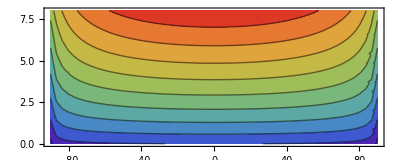

```mathematica
ContourPlot[0.01134585054552213 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,7}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,7}]),{zm,-90,90},{ym,0,8},Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

```mathematica
velFebbraio[zm_,ym_] = J[zm,ym,180,5]/Sum[J[zm,ym,180,5], {ym,0,5},{zm,-90,90}] *7/0.01
```

NIntegrate::inumr: The integrand (90+zm)/(((-y+ym)^2+(90+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5}}.

NIntegrate::inumr: The integrand (90-zm)/(((-y+ym)^2+(90-zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5}}.

NIntegrate::inumr: The integrand ym/((ym^2+(-z+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-90,90}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.0142787 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,5}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,5}])

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-89.9752030796111804400450040475334390066564083099365234375}. NIntegrate obtained 0.00524474 and 0.000301066 for the integral and error estimates.

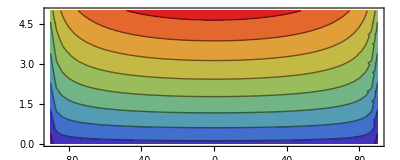

```mathematica
ContourPlot[0.014278699491933196 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,5}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,5}]),{zm,-90,90},{ym,0,5},Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

```mathematica
velMarzo[zm_,ym_] = J[zm,ym,180,5]/Sum[J[zm,ym,180,5], {ym,0,5},{zm,-90,90}] *6/0.01
```

NIntegrate::inumr: The integrand (90+zm)/(((-y+ym)^2+(90+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5}}.

NIntegrate::inumr: The integrand (90-zm)/(((-y+ym)^2+(90-zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5}}.

NIntegrate::inumr: The integrand ym/((ym^2+(-z+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-90,90}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.0122389 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,5}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,5}])

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-89.9752030796111804400450040475334390066564083099365234375}. NIntegrate obtained 0.00524474 and 0.000301066 for the integral and error estimates.

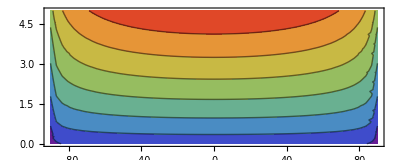

```mathematica
ContourPlot[0.012238885278799882 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,5}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,5}]),{zm,-90,90},{ym,0,5},Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

```mathematica
velAprile[zm_,ym_] =  J[zm,ym,180,7]/Sum[J[zm,ym,180,7], {ym,0,7},{zm,-90,90}] *10/0.01
```

NIntegrate::inumr: The integrand (90+zm)/(((-y+ym)^2+(90+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,7}}.

NIntegrate::inumr: The integrand (90-zm)/(((-y+ym)^2+(90-zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,7}}.

NIntegrate::inumr: The integrand ym/((ym^2+(-z+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-90,90}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.0113459 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,7}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,7}])

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-89.9752030796111804400450040475334390066564083099365234375}. NIntegrate obtained 0.00716732 and 0.000266387 for the integral and error estimates.

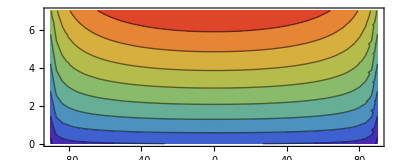

```mathematica
ContourPlot[0.01134585054552213 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,7}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,7}]),{zm,-90,90},{ym,0,7},Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

```mathematica
velMaggio[zm_,ym_] = J[zm,ym,180,10]/Sum[J[zm,ym,180,10], {ym,0,10},{zm,-90,90}] *19/0.01
```

NIntegrate::inumr: The integrand (90+zm)/(((-y+ym)^2+(90+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,10}}.

NIntegrate::inumr: The integrand (90-zm)/(((-y+ym)^2+(90-zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,10}}.

NIntegrate::inumr: The integrand ym/((ym^2+(-z+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-90,90}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.0114758 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,10}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,10}])

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-89.9752030796111804400450040475334390066564083099365234375}. NIntegrate obtained 0.0100238 and 0.00021645 for the integral and error estimates.

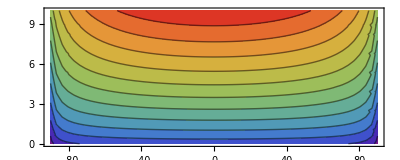

```mathematica
ContourPlot[0.01147580104179343 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,10}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,10}]),{zm,-90,90},{ym,0,10},Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

```mathematica
velGiugno[zm_,ym_] = J[zm,ym,180,13]/Sum[J[zm,ym,180,13], {ym,0,13},{zm,-90,90}] *27/0.01
```

NIntegrate::inumr: The integrand (90+zm)/(((-y+ym)^2+(90+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,13}}.

NIntegrate::inumr: The integrand (90-zm)/(((-y+ym)^2+(90-zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,13}}.

NIntegrate::inumr: The integrand ym/((ym^2+(-z+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-90,90}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.0102206 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,13}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,13}])

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-89.9752030796111804400450040475334390066564083099365234375}. NIntegrate obtained 0.0128493 and 0.000174548 for the integral and error estimates.

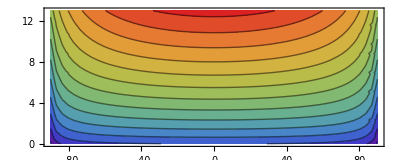

```mathematica
ContourPlot[0.010220628642319443 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,13}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,13}]),{zm,-90,90},{ym,0,13},Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

```mathematica
velLuglio[zm_,ym_] = J[zm,ym,180,14]/Sum[J[zm,ym,180,14], {ym,0,14},{zm,-90,90}] *31/0.01
```

NIntegrate::inumr: The integrand (90+zm)/(((-y+ym)^2+(90+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,14}}.

NIntegrate::inumr: The integrand (90-zm)/(((-y+ym)^2+(90-zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,14}}.

NIntegrate::inumr: The integrand ym/((ym^2+(-z+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-90,90}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.0102808 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,14}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,14}])

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-89.9752030796111804400450040475334390066564083099365234375}. NIntegrate obtained 0.0137845 and 0.000162661 for the integral and error estimates.

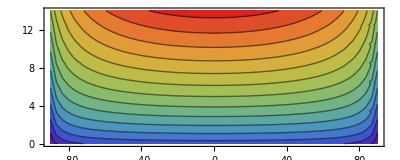

```mathematica
ContourPlot[0.010280765235115018 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,14}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,14}]),{zm,-90,90},{ym,0,14},Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

```mathematica
velAgosto[zm_,ym_] = J[zm,ym,180,13]/Sum[J[zm,ym,180,13], {ym,0,13},{zm,-90,90}] *26/0.01
```

NIntegrate::inumr: The integrand (90+zm)/(((-y+ym)^2+(90+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,13}}.

NIntegrate::inumr: The integrand (90-zm)/(((-y+ym)^2+(90-zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,13}}.

NIntegrate::inumr: The integrand ym/((ym^2+(-z+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-90,90}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.00984209 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,13}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,13}])

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-89.9752030796111804400450040475334390066564083099365234375}. NIntegrate obtained 0.0128493 and 0.000174548 for the integral and error estimates.

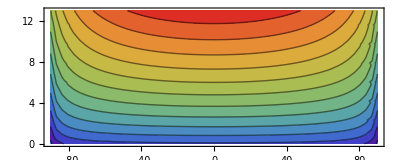

```mathematica
ContourPlot[0.009842086840752056 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,13}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,13}]),{zm,-90,90},{ym,0,13},Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

```mathematica
velSettembre[zm_,ym_] = J[zm,ym,180,12]/Sum[J[zm,ym,180,12], {ym,0,12},{zm,-90,90}] *23/0.01
```

NIntegrate::inumr: The integrand (90+zm)/(((-y+ym)^2+(90+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,12}}.

NIntegrate::inumr: The integrand (90-zm)/(((-y+ym)^2+(90-zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,12}}.

NIntegrate::inumr: The integrand ym/((ym^2+(-z+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-90,90}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.0100424 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,12}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,12}])

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-89.9752030796111804400450040475334390066564083099365234375}. NIntegrate obtained 0.0119108 and 0.00018748 for the integral and error estimates.

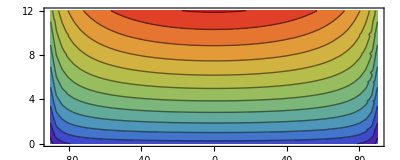

```mathematica
ContourPlot[0.010042414335104125 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,12}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,12}]),{zm,-90,90},{ym,0,12},Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

```mathematica
velOttobre[zm_,ym_] = J[zm,ym,180,8]/Sum[J[zm,ym,180,8], {ym,0,8},{zm,-90,90}] *12/0.01
```

NIntegrate::inumr: The integrand (90+zm)/(((-y+ym)^2+(90+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,8}}.

NIntegrate::inumr: The integrand (90-zm)/(((-y+ym)^2+(90-zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,8}}.

NIntegrate::inumr: The integrand ym/((ym^2+(-z+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-90,90}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.0107615 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,8}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,8}])

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-89.9752030796111804400450040475334390066564083099365234375}. NIntegrate obtained 0.008123 and 0.000249098 for the integral and error estimates.

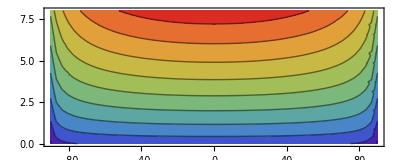

```mathematica
ContourPlot[0.010761505919079718 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,8}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,8}]),{zm,-90,90},{ym,0,8},Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

```mathematica
velNovembre[zm_,ym_] =J[zm,ym,180,8]/Sum[J[zm,ym,180,8], {ym,0,8},{zm,-90,90}] *13/0.01
```

NIntegrate::inumr: The integrand (90+zm)/(((-y+ym)^2+(90+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,8}}.

NIntegrate::inumr: The integrand (90-zm)/(((-y+ym)^2+(90-zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,8}}.

NIntegrate::inumr: The integrand ym/((ym^2+(-z+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-90,90}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.0116583 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,8}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,8}])

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-89.9752030796111804400450040475334390066564083099365234375}. NIntegrate obtained 0.008123 and 0.000249098 for the integral and error estimates.

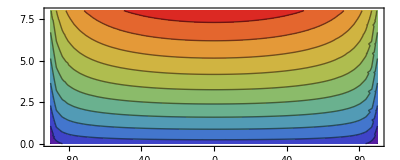

```mathematica
ContourPlot[0.011658298079003027 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,8}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,8}]),{zm,-90,90},{ym,0,8},Contours->{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.0,2.1,2.2,2.3}, ContourShading->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,AspectRatio->2/5]
```

```mathematica
velDicembre[zm_,ym_] = J[zm,ym,180,8]/Sum[J[zm,ym,180,8], {ym,0,8},{zm,-90,90}] *12/0.01
```

NIntegrate::inumr: The integrand (90+zm)/(((-y+ym)^2+(90+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,8}}.

NIntegrate::inumr: The integrand (90-zm)/(((-y+ym)^2+(90-zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,8}}.

NIntegrate::inumr: The integrand ym/((ym^2+(-z+zm)^2)^(3/7)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-90,90}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.0107615 (NIntegrate[ym (√((zm-z)^2+ym^2))^(-6/7),{z,-180/2,180/2}]+NIntegrate[(180/2-zm) (√((ym-y)^2+(180/2-zm)^2))^(-6/7),{y,0,8}]+NIntegrate[(180/2+zm) (√((ym-y)^2+(180/2+zm)^2))^(-6/7),{y,0,8}])